```mathematica
ClearAll[unblendedCircleSmoothie]

unblendedCircleSmoothie[function_,variable_Symbol,numCir_Integer]:=
	Block[
		{
			fourierCoeff=Table[FourierCosCoefficient[function,variable,p],{p,1,numCir}],
			color=Drop[Hue[#]&/@Range[0,1,(1/numCir)],-1],
			circleList,basicCoord,manipulatedCoord,maxRadius,lineList,plotList,styledLines,prePlot
		},
		circleList=Circle[{-maxRadius-5,0},#1]&/@Abs@fourierCoeff;
		basicCoord=MapThread[Times,{fourierCoeff,Cos[Range[numCir]*variable]}];
		manipulatedCoord=Transpose[{basicCoord-maxRadius-5,basicCoord/.Cos->Sin}];
		maxRadius=Max[Abs@fourierCoeff];
		lineList=Line[{{-maxRadius-5,0},#1,{0,#1[[2]]}}]&/@manipulatedCoord/.variable->$time;
		styledLines=MapThread[Style,{lineList,color}];
		
		prePlot=MapThread[Times,{fourierCoeff,Cos[(Range[numCir]*(variable+$time))-(Pi/2)]}];
		plotList=Plot[#1,{variable,0,10},PlotStyle->#2]&@@@(Transpose[{prePlot,color}]);
		
		Animate[
			Show[
				Graphics[{Sequence@@#1,Sequence@@#2},Axes->True],
				Plot[#3,{variable,0,10},PlotStyle->#4,PlotRange->All],PlotRange->All
				],
		{$time,0,-2Pi},AnimationRunning->False]&@@Evaluate[{circleList,styledLines,prePlot,color}]
	
	]
```

```mathematica
fourierCoeff=Table[FourierCosCoefficient[function,variable,p],{p,1,numCir}]
MapThread[Times,{fourierCoeff,Cos[Range[numCir]*variable]}]
```

```mathematica
FourierCosCoefficient[Sqrt[x-5],x,2]//Abs
```

1/(2 π √(2/((Im[Gamma[3/2,-10 ⅈ]-Gamma[3/2,2 ⅈ (-5+π)]]+Cos[20] Re[Gamma[3/2,10 ⅈ]-Gamma[3/2,-2 ⅈ (-5+π)]]-Im[Gamma[3/2,10 ⅈ]-Gamma[3/2,-2 ⅈ (-5+π)]] Sin[20])^2+(-Cos[20] Im[Gamma[3/2,10 ⅈ]-Gamma[3/2,-2 ⅈ (-5+π)]]+Re[Gamma[3/2,-10 ⅈ]-Gamma[3/2,2 ⅈ (-5+π)]]-Re[Gamma[3/2,10 ⅈ]-Gamma[3/2,-2 ⅈ (-5+π)]] Sin[20])^2)))

```mathematica
unblendedCircleSmoothie[x^2+5x-3,x,15]
```

```mathematica
ClearAll[protocircleSmoothie]

protocircleSmoothie[function_,variable_Symbol,numCir_Integer]:=
	Block[
		{
			fourierCoeff=Table[FourierCosCoefficient[function,variable,p],{p,1,numCir}],
			color=Drop[Hue[#]&/@Range[0,1,(1/numCir)],-1],
			circleList,basicCoord,manipulatedCoord,maxRadius,lineList,plotList,styledLines,prePlot,lastCoordinate
		},
		
		maxRadius=Max[Abs@fourierCoeff];
		basicCoord=MapThread[Times,{fourierCoeff,Cos[Range[5]*x]}];
		manipulatedCoord=Join[Take[Transpose[{basicCoord-maxRadius-5,basicCoord/.Cos->Sin}],1],Drop[Transpose[{basicCoord,basicCoord/.Cos->Sin}],1]];
		manipulatedCoord=(Plus@@@Table[
								manipulatedCoord[[;;n]],
								{n,1,Length[manipulatedCoord]}]//Prepend[{0,0}]);
		
		
		lineList=Line[#1]&@Prepend[Drop[manipulatedCoord,1],{-maxRadius-5,0}]/.variable->$time;
	
		circleList=Circle[#1,#2]&@@@{manipulatedCoord,Abs@fourierCoeff};
		prePlot=MapThread[Times,{fourierCoeff,Cos[(Range[numCir]*(variable+$time))-(Pi/2)]}];
		lastCoordinate=(Take[Take[manipulatedCoord,-1]//Flatten,1]+maxRadius+5)/.variable->(variable+$time);
		plotList=Plot[#1,{variable,0,10}]&@lastCoordinate;
		
		Animate[
			Show[
				Graphics[{Sequence@@#1,Sequence@@#2},Axes->True],
				#3,PlotRange->All
				],
		{$time,0,-2Pi},AnimationRunning->False]&@@Evaluate[{circleList,lineList,plotList}]
		]
```

```mathematica
Plot[(Take[Take[manipulatedCoord,-1]//Flatten,1]+maxRadius+5)/.x->(x+$time)]
```

Plot::argr: Plot called with 1 argument; 2 arguments are expected.

Plot[Take[Flatten[Take[manipulatedCoord,-1]],1]+maxRadius+5/.x→x+$time]

```mathematica
Take[Transpose[{basicCoord-maxRadius-5,basicCoord/.Cos->Sin}],1]
```

{{-9-4 Cos[x],-4 Sin[x]}}

```mathematica
Drop[Transpose[{basicCoord-maxRadius-5,basicCoord/.Cos->Sin}],1]
```

{{-9+Cos[2 x],Sin[2 x]},{-9-4/9 Cos[3 x],-4/9 Sin[3 x]},{-9+1/4 Cos[4 x],1/4 Sin[4 x]},{-9-4/25 Cos[5 x],-4/25 Sin[5 x]}}

```mathematica
lastCoordinate=(Take[Take[manipulatedCoord,-1]//Flatten,1]+maxRadius+5)/.x->(x+time)
```

```mathematica
fourierCoeff=Table[FourierCosCoefficient[x^2,x,p],{p,1,5}]
maxRadius=Max[Abs@fourierCoeff];
basicCoord=MapThread[Times,{fourierCoeff,Cos[Range[5]*x]}]
manipulatedCoord=Join[Take[Transpose[{basicCoord-maxRadius-5,basicCoord/.Cos->Sin}],1],Drop[Transpose[{basicCoord,basicCoord/.Cos->Sin}],1]]
manipulatedCoord=(Plus@@@Table[
								manipulatedCoord[[;;n]],
								{n,1,Length[manipulatedCoord]}]//Prepend[{0,0}])
Take[Take[manipulatedCoord,-1]//Flatten,1]+maxRadius+5
```

{-4,1,-4/9,1/4,-4/25}

{-4 Cos[x],Cos[2 x],-4/9 Cos[3 x],1/4 Cos[4 x],-4/25 Cos[5 x]}

{{-9-4 Cos[x],-4 Sin[x]},{Cos[2 x],Sin[2 x]},{-4/9 Cos[3 x],-4/9 Sin[3 x]},{1/4 Cos[4 x],1/4 Sin[4 x]},{-4/25 Cos[5 x],-4/25 Sin[5 x]}}

{{0,0},{-9-4 Cos[x],-4 Sin[x]},{-9-4 Cos[x]+Cos[2 x],-4 Sin[x]+Sin[2 x]},{-9-4 Cos[x]+Cos[2 x]-4/9 Cos[3 x],-4 Sin[x]+Sin[2 x]-4/9 Sin[3 x]},{-9-4 Cos[x]+Cos[2 x]-4/9 Cos[3 x]+1/4 Cos[4 x],-4 Sin[x]+Sin[2 x]-4/9 Sin[3 x]+1/4 Sin[4 x]},{-9-4 Cos[x]+Cos[2 x]-4/9 Cos[3 x]+1/4 Cos[4 x]-4/25 Cos[5 x],-4 Sin[x]+Sin[2 x]-4/9 Sin[3 x]+1/4 Sin[4 x]-4/25 Sin[5 x]}}

{-4 Cos[x]+Cos[2 x]-4/9 Cos[3 x]+1/4 Cos[4 x]-4/25 Cos[5 x]}

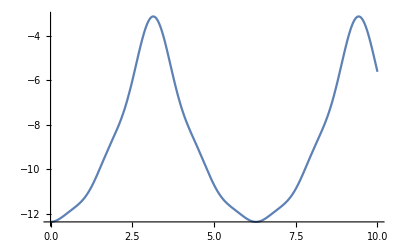
9+-Graphics-

```mathematica
Plot[#1,{x,0,10}]&@Take[Take[manipulatedCoord,-1]//Flatten,1]+maxRadius+5
```

```mathematica
lineList=Line[#1]&@Prepend[Drop[manipulatedCoord,1],{-maxRadius-5,0}]/.variable->$tim
```

Line[{{-9,0},{-9-4 Cos[x],-4 Sin[x]},{-9-4 Cos[x]+Cos[2 x],-4 Sin[x]+Sin[2 x]},{-9-4 Cos[x]+Cos[2 x]-4/9 Cos[3 x],-4 Sin[x]+Sin[2 x]-4/9 Sin[3 x]},{-9-4 Cos[x]+Cos[2 x]-4/9 Cos[3 x]+1/4 Cos[4 x],-4 Sin[x]+Sin[2 x]-4/9 Sin[3 x]+1/4 Sin[4 x]},{-9-4 Cos[x]+Cos[2 x]-4/9 Cos[3 x]+1/4 Cos[4 x]-4/25 Cos[5 x],-4 Sin[x]+Sin[2 x]-4/9 Sin[3 x]+1/4 Sin[4 x]-4/25 Sin[5 x]}}]

```mathematica
circleSmoothie[x^2,x,5]
```

```mathematica
circleTest2=Circle[{-7,0},#1]&/@Abs@Table[FourierCosCoefficient[x^2,x,p],{p,1,5}];
	Animate[
		Show[
			Graphics[{#1,
				Style[Line[{{-7,0},{-4Cos[t]-7,-4Sin[t]},{0,-4Sin[t]}}],Red],
				Style[Line[{{-7,0},{Cos[-2t]-7,Sin[-2t]},{0,Sin[-2t]}}],Green],
				Style[Line[{{-7,0},{-(4/9)Cos[-3t]-7,(-4/9)Sin[-3t]},{0,(-4/9)Sin[-3t]}}],Blue]}
			,Axes->True],
			{
			Plot[-4Cos[x+t-(Pi/2)],{x,0,10},PlotStyle->Red],
			Plot[Cos[-2(x+t-(3Pi/4))],{x,0,10},PlotStyle->Green],
			Plot[-(4/9)Cos[-3(x+t-(Pi/2))],{x,0,10},PlotStyle->Blue]
			
			}
			
	],{t,0,-2Pi},AnimationRunning->False]&@circleTest2
```

```mathematica
circleTest2=Echo@Circle[{-7,0},#1]&/@Abs@Table[FourierCosCoefficient[x^2,x,p],{p,1,5}];
	Animate[
		Show[
			Graphics[{
				(*A list of circles with centers so 
				Circle[center,radius]
				*)
				Circle[{-7,0},4],
				Circle[{-4Cos[t]-7,-4Sin[t]},1],
				Circle[{-4Cos[t]+Cos[-2t]-7,-4Sin[t]+Sin[-2t]},4/9],
				(* One line with a list of coordinates,starting form the center of the first circle going to the edge of the last one. 
					Then the last coordinate is going to be from the edge to the Y-axis
				Line[
				{CenterOfFirstCircle,listOfCoordinates,lastCircleToYAxes}
				]
				lastCircleToYAxes={0,lastYCoord}
				*)
				Line[{
						{-7,0},{-4Cos[t]-7,-4Sin[t]},
						{-4Cos[t]+Cos[-2t]-7,-4Sin[t]+Sin[-2t]},
						{-4Cos[t]+Cos[-2t]-(4/9)Cos[-3t]-7,-4Sin[t]+Sin[-2t]-4/9Sin[-3t]},
						{0,-4Sin[t]+Sin[-2t]-4/9Sin[-3t]}
					}]}
			,Axes->True],
			{
			(*Plot will be the entire function added up,
				Plot[LastXCoord,{variable,0,10}]			
			*)
			Plot[-4Cos[x+t-(Pi/2)]+Cos[-2(x+t)-(Pi/2)]-(4/9)Cos[-3(x+t)-(Pi/2)],{x,0,10}]
			}
			
	],{t,0,-2Pi},AnimationRunning->False]
	
	(*Making the consecutive list
	Step 1: List of the coordinates will be generated by articifally generaing each one first
		fourierCoeff=Table[FourierCosCoefficient[function,variable,p],{p,1,numCir}]
		basicCoord=MapThread[Times,{fourierCoeff,Cos[Range[numCir]*variable]}]
	
	Step 2: Then generate the list so that only the first coordinate's x-value is subtracted by (maxradius+buffer)	
		manipulatedCoord=Join[Take[Transpose[{basicCoord-maxRadius-5,basicCoord/.Cos->Sin}],1],Drop[Transpose[{basicCoord,basicCoord/.Cos->Sin}],1]]
	
	Step 3: Now create a coordinate list where all previous terms are also included within the other values
		Ex: {{-7,0},{-4Cos[t]-7,-4Sin[t]},
			{-4Cos[t]+Cos[-2t]-7,-4Sin[t]+Sin[-2t]},
			{-4Cos[t]+Cos[-2t]-(4/9)Cos[-3t]-7,-4Sin[t]+Sin[-2t]-4/9Sin[-3t]}}
		Method: 
			manipulatedCoord=(Plus@@@Table[
								manipulatedCoord[[;;n]],
								{n,1,Length[manipulatedCoord]}]//Prepend[{-maxradius-5,0}])
	
	Step 4: For the last coordinate of the list we need to Append (0,lastYValue)
		Take[Take[manipulatedCoord,-1]//Flatten,-1]
	*)
```

Circle[{-7,0},4]

Circle[{-7,0},1]

Circle[{-7,0},4/9]

Circle[{-7,0},1/4]

Circle[{-7,0},4/25]

```mathematica
Table[FourierCosCoefficient[x^2,x,p],{p,1,5}]
```

{-4,1,-4/9,1/4,-4/25}

```mathematica
{{ClearAll[circleSmoothie]

circleSmoothie[function_,variable_Symbol,numCir_Integer]:=
	Block[{
		fourierCoeff=Table[FourierCosCoefficient[function,variable,p],{p,1,numCir}],
		basicCoord,manipulatedCoord,lastYCoord,maxRadius,combinedCir,cirCenter,cirArguments,finalPlot,lineSeries,centerOfFirstCir,listOfCoord,lastLinetoYaxis,lastXCoord
	
	
	},
	
	maxRadius=Max[Abs@fourierCoeff];
	basicCoord=MapThread[Times,{fourierCoeff,Cos[Range[numCir]*variable]}];
	manipulatedCoord=Join[Take[Transpose[{basicCoord-maxRadius-5,basicCoord/.Cos->Sin}],1],Drop[Transpose[{basicCoord,basicCoord/.Cos->Sin}],1]];
	manipulatedCoord=(Plus@@@Table[
								manipulatedCoord[[;;n]],
								{n,1,Length[manipulatedCoord]}]//Prepend[{-maxRadius-5,0}]);
	manipulatedCoord=manipulatedCoord/.variable->($time);
	lastYCoord={0,Take[Take[manipulatedCoord,-1]//Flatten,-1]};
	cirCenter=Drop[manipulatedCoord,-1];
	cirArguments=Transpose[{cirCenter,Abs@fourierCoeff}];
	combinedCir={Circle[#1,#2]}&@@@#1&/@cirArguments;
	lastLinetoYaxis={0,Take[Take[manipulatedCoord,-1]//Flatten,-1]};
	
	lineSeries= Line[{manipulatedCoord,lastLinetoYaxis}];
	
	lastXCoord=Take[Take[manipulatedCoord,-1]//Flatten,1];
	finalPlot=Plot[lastXCoord,{variable,0,10}];
	
	Print[lineSeries];
	Print[manipulatedCoord];
	Print[#1&/@cirArguments];
	
	Animate[
			Show[
				Graphics[{Sequence@@#1,Sequence@@#2},Axes->True],
				#3,PlotRange->All
				],
		{$time,0,-2Pi},AnimationRunning->False]&@@Evaluate[{combinedCir,lineSeries,finalPlot}]
	
	
	]}, {□}}
```

{{Null^2},{□}}

```mathematica
Animate[
		Show[
			Graphics[{
				(*A list of circles with centers so 
				Circle[center,radius]
				*)
				Circle[{-7,0},4],
				Circle[{-4Cos[t]-7,-4Sin[t]},1],
				Circle[{-4Cos[t]+Cos[-2t]-7,-4Sin[t]+Sin[-2t]},4/9],
				(* One line with a list of coordinates,starting form the center of the first circle going to the edge of the last one. 
					Then the last coordinate is going to be from the edge to the Y-axis
				Line[
				{CenterOfFirstCircle,listOfCoordinates,lastCircleToYAxes}
				]
				lastCircleToYAxes={0,lastYCoord}
				*)
				Line[{
						{-7,0},{-4Cos[t]-7,-4Sin[t]},
						{-4Cos[t]+Cos[-2t]-7,-4Sin[t]+Sin[-2t]},
						{-4Cos[t]+Cos[-2t]-(4/9)Cos[-3t]-7,-4Sin[t]+Sin[-2t]-4/9Sin[-3t]},
						{0,-4Sin[t]+Sin[-2t]-4/9Sin[-3t]}
					}]}
			,Axes->True],
			{
			(*Plot will be the entire function added up,
				Plot[LastXCoord,{variable,0,10}]			
			*)
			Plot[-4Cos[x+t-(Pi/2)]+Cos[-2(x+t)-(Pi/2)]-(4/9)Cos[-3(x+t)-(Pi/2)],{x,0,10}]
			}
			
	],{t,0,-2Pi},AnimationRunning->False]
```

```mathematica
Circle[#1,#2]&@@@{{{-9,0},4},{{-9-4 Cos[x],-4 Sin[x]},1},{{-9-4 Cos[x]+Cos[2 x],-4 Sin[x]+Sin[2 x]},4/9},{{-9-4 Cos[x]+Cos[2 x]-4/9 Cos[3 x],-4 Sin[x]+Sin[2 x]-4/9 Sin[3 x]},1/4},{{-9-4 Cos[x]+Cos[2 x]-4/9 Cos[3 x]+1/4 Cos[4 x],-4 Sin[x]+Sin[2 x]-4/9 Sin[3 x]+1/4 Sin[4 x]},4/25}}
```

{Circle[{-9,0},4],Circle[{-9-4 Cos[x],-4 Sin[x]},1],Circle[{-9-4 Cos[x]+Cos[2 x],-4 Sin[x]+Sin[2 x]},4/9],Circle[{-9-4 Cos[x]+Cos[2 x]-4/9 Cos[3 x],-4 Sin[x]+Sin[2 x]-4/9 Sin[3 x]},1/4],Circle[{-9-4 Cos[x]+Cos[2 x]-4/9 Cos[3 x]+1/4 Cos[4 x],-4 Sin[x]+Sin[2 x]-4/9 Sin[3 x]+1/4 Sin[4 x]},4/25]}